# Building Blocks of Quantum Circuits

We will review the common procedure for a quantum algorithm: a state is prepared, some quantum operations are done, and then measurements. We will show how this is done within an object usually called quantum circuit. We will discuss each concept, eg quantum state, quantum operator, quantum basis and etc more.

## Key Concepts

Quantum State

Register State

Quantum Operator

Bloch Sphere

Computational Basis

## Quantum Operations

In the last lesson, you saw the following quantum circuit:

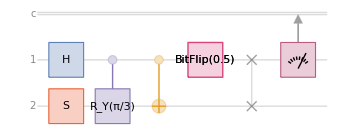

```mathematica
QuantumCircuitOperator[{"H","S"->2,"C"["RY"[π/3]]->{1,2},"CNOT","BitFlip","SWAP",{1}}]["Diagram"]
```

In classical computation, we use rules to map input states to output states. Quantum operators serve a similar role: they are the rules that transform one quantum state into another. Unlike classical rules, however, they must obey specific constraints set by the formalism of quantum mechanics; for example, they are linear and usually unitary. In the language of quantum computing, you will often hear these operators described as “gates” or “gate operations.” This terminology is borrowed from classical computer engineering.

## Quantum States

In classical digital computing, states are represented by sequences of 1s and 0s. Each classical bit has two possible states, 0 or 1. A sequence of two bits has four possible states: “00,” “01,” “10,” or “11. In general, a sequence of n classical bits has 2^n possible states.

Quantum states behave differently. When a quantum state is measured, the outcome is always a definite classical result. However, the act of measurement inevitably changes the state, this is known as state collapse. Unlike classical states, quantum states can exist in superpositions. Still, there are special quantum states called computational basis states that always yield the same classical result when measured. These states can be labeled directly by a classical bit string.

If quantum operators in a circuit diagram are the instructions for changing a state, what do we assume about the input state? By convention, most quantum circuit diagrams begin with the register state. This is the special basis state that always yields the classical result of all zeros when the qubits are measured.

The 1-qubit register state can be written as follows:

```mathematica
QuantumState["Register"]["Formula"]
```

0

The 2-qubit register state can be written like this:

```mathematica
QuantumState["Register"[2]]["Formula"]
```

00

And so on:

```mathematica
Table[QuantumState["Register"[n]]["Formula"],{n,3,6}]
```

{000,0000,00000,000000}

Throughout this course, we will follow big-endian (usual Dirac) convention, as opposed to little-endian (usual IBM) convention. In the big endian convention, a state such as 01 means qubit-1 is in the state 0 and qubit-2 is in the state 1.

While some quantum states always give the same result for the same measurements, it is important to remember that this is not the case for all quantum states. Future examples will examine this in more detail.

## The Bloch Sphere

Since qubits are not the same as classical bits, labeling them by classical bit sequences is insufficient to represent all possible qubit states. How then are quantum states represented?

Future lessons will discuss representing quantum states with matrices. In fact, much of the formalism of quantum mechanics is an important application of linear algebra. However, there is a very useful graphical representation of 1-qubit states called the Bloch sphere.

The Bloch sphere is named after physicist Felix Bloch:

-Graphics-

The Bloch sphere representation of the qubit state 0 can be given as follows:

```mathematica
QuantumState["0"]["BlochPlot"]
```

-Graphics3D-

Notice that the qubit state 1 is on the opposite side of the sphere from 0.

```mathematica
QuantumState["1"]["BlochPlot"]
```

-Graphics3D-

The use of the sphere already suggests that the space of 1-qubit states is already quite a bit richer than only 0 or 1 as in classical bits. The states labeled +, -, L and R are other specific states the qubits can attain. However, the 0 and 1 states are usually called the computational basis states. In order to read out a result from the qubits that can be used in digital computation, you must measure the state of the qubit in the chosen computational basis.

Physically, there is some arbitrariness in how the states on the Bloch sphere are labeled. What matters is that the designer of a quantum computer chooses two easily measurable quantum states to serve as the logical values of a classical 0 and a classical 1. Quantum operations can then rotate or transform qubits into other states on the Bloch sphere; this ability is precisely what makes quantum computation more powerful than classical computation. In practice, however, the final step in a quantum circuit is always to measure the qubits in the chosen computational basis, so that the result can be expressed in classical bits.

Bloch vector of a random state:

```mathematica
state=QuantumState["RandomPure"];
Grid[Transpose[{{"Formula","Bloch vector","Bloch spherical coordinates","Bloch plot"},{TraditionalForm[state],state["BlochVector"],state["BlochSphericalCoordinates"],state["BlochPlot"]}}],Frame->All,Alignment->Left]
```

Formula | (0.778077+0.227599 ⅈ)0+(-0.423022-0.404779 ⅈ)1
Bloch vector | {-0.842543,-0.437341,0.314411}
Bloch spherical coordinates | {1,1.25096,-2.6628}
Bloch plot | -Graphics3D-

## Effects of Operations on Qubits

Consider the following circuit:

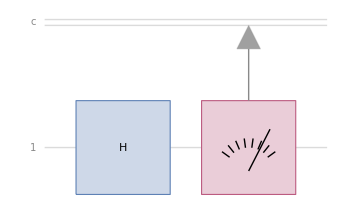

```mathematica
QuantumCircuitOperator[{"H",{1}}]["Diagram"]
```

Let’s examine these operations in more detail. The gate labeled “H” is called a Hadamard gate, named after French mathematician Jacques Salomon Hadamard.

-Graphics-

What is the effect of this gate on a qubit in the register state?

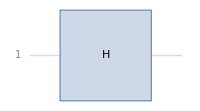
-Graphics- ⇒ -Graphics3D-

```mathematica
With[{circuit=QuantumCircuitOperator[{"H"->1}],size=200},
Row[{circuit["Diagram",ImageSize->{size,Automatic}],circuit[]["BlochPlot",ImageSize->size]},Style[" ⇒ ",Bold,20]]
]
```

Notice that the qubit is no longer in either the 0 or 1 state. What will happen if you add a measurement in the computational basis?

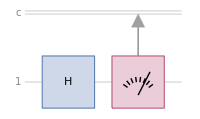
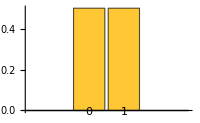
-Graphics- ⇒ -Graphics-

```mathematica
With[{circuit=QuantumCircuitOperator[{"H"->1,"M"->1}],size=200},
Row[{circuit["Diagram",ImageSize->{size,Automatic}],circuit[]["ProbabilityPlot",ImageSize->size]},Style[" ⇒ ",Bold,20]]
]
```

After applying a Hadamard gate to the register state and measuring, you will have a 50-50 chance of obtaining the 0 or 1 outcomes. Notice the connection between the geometry of the Bloch sphere and these probabilities. After applying the Hadamard gate to the register state, the qubit’s state is “in the middle” of the 0/1 axis on the Bloch sphere. Measuring in the computational basis changes the state of the qubit to be either 0 or 1, with equal probability in this case.

### A Quick Note on Measurement

You might wonder at what point probabilities enter the picture. Does the Hadamard gate introduce the need for probability or does the measurement? Before answering this question, what happens if the measurement is not done in the computational basis? What happens if a different measurement is performed with a special relationship to the Hadamard gate as shown below?

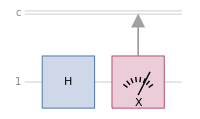
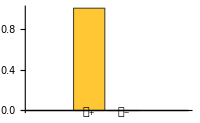
-Graphics- ⇒ -Graphics-

```mathematica
With[{circuit=QuantumCircuitOperator[{"H"->1,"M"["X"]->1}],size=200},
Row[{circuit["Diagram",ImageSize->{size,Automatic}],circuit[]["ProbabilitiesPlot",ImageSize->size]},Style[" ⇒ ",Bold,20]]
]
```

Performing this new measurement (not the usual computational basis) gives the same result with 100% probability after applying the Hadamard gate. Thus, there are cases where measurement also does not lead to probabilistic results.

As shown in the Bloch plot, the qubit is in a definite quantum state after the Hadamard gate is applied:

```mathematica
With[{circuit=QuantumCircuitOperator[{"H"->1}],size=200},
Row[{circuit["Diagram",ImageSize->{size,Automatic}],circuit[]["BlochPlot",ImageSize->size]},Style[" ⇒ ",Bold,20]]
]
```

-Graphics- ⇒ -Graphics3D-

Measuring this particular qubit state along the +/- axis will always give the same result, as you saw from the plot of measurement probabilities.

Probability is only necessary when the quantum state before measurement is not in the same basis as the measurement being performed. If you want to know precise details about this feature of quantum mechanics, it is typically expressed in terms of eigenvalues and eigenvectors of matrices. You can learn about this mathematical formalism in a course on linear algebra.

## More Operations on Qubits

You have seen the effects of the Hadamard gate. What about the “NOT” operation?

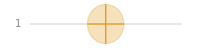
-Graphics- ⇒ -Graphics3D-

```mathematica
With[{circuit=QuantumCircuitOperator[{"NOT"->1}],size=200},
Row[{circuit["Diagram",ImageSize->{size,Automatic}],circuit[]["BlochPlot",ImageSize->size]},Style[" ⇒ ",Bold,20]]
]
```

Unsurprisingly, applying the “NOT” operation to the register state changes 0 to 1 with 100% probability.

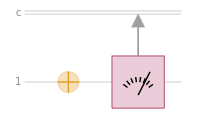
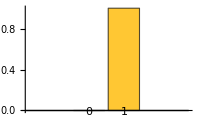
-Graphics- ⇒ -Graphics-

```mathematica
With[{circuit=QuantumCircuitOperator[{"NOT"->1,"M"->1}],size=200},
Row[{circuit["Diagram",ImageSize->{size,Automatic}],circuit[]["ProbabilitiesPlot",ImageSize->size]},Style[" ⇒ ",Bold,20]]
]
```

Many important operations involve more than one qubit. One of the simplest is the “SWAP” operation. This just re-labels the qubits by swapping two of them:

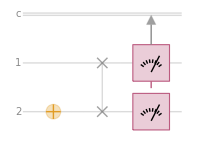
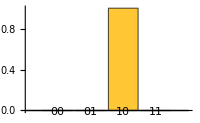
-Graphics- ⇒ -Graphics-

```mathematica
With[{circuit=QuantumCircuitOperator[{"NOT"->2,"SWAP"->{1,2},"M"->{1,2}}]},
Row[{circuit["Diagram",ImageSize->{200,Automatic}],circuit[]["ProbabilitiesPlot",ImageSize->200]},Style[" ⇒ ",Bold,20]]
]
```

Notice how the results of this circuit are always the bit sequence “10”, even though the “NOT” operation was applied to the 2nd qubit. That’s because a “SWAP” is performed just after the “NOT” operation. Contrast this with the unswapped case:

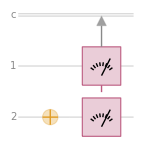
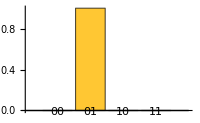
-Graphics- ⇒ -Graphics-

```mathematica
With[{circuit=QuantumCircuitOperator[{"NOT"->2,"M"->{1,2}}]},
Row[{circuit["Diagram",ImageSize->{200,Automatic}],circuit[]["ProbabilitiesPlot",ImageSize->200]},Style[" ⇒ ",Bold,20]]
]
```

Controlled operations are another important category. One of the most common examples is the controlled not gate or “CNOT”:

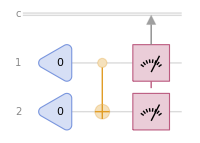
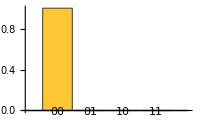
-Graphics- ⇒ -Graphics-

```mathematica
With[{circuit=QuantumCircuitOperator[{"0","0"->2,"CNOT"->{1,2},"M"->{1,2}}]},
Row[{circuit["Diagram",ImageSize->{200,Automatic}],circuit[]["ProbabilitiesPlot",ImageSize->200]},Style[" ⇒ ",Bold,20]]
]
```

On this particular input, “CNOT” does not appear to do anything. That’s because a controlled gate can be thought of like an “if” statement. If the control qubit is a “1”, perform an operation on the target qubit. If the control qubit is a “0”, do nothing.

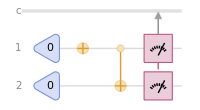
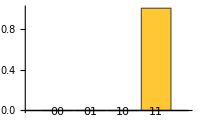
-Graphics- ⇒ -Graphics-

```mathematica
With[{circuit=QuantumCircuitOperator[{"0","0"->2,"NOT","CNOT"->{1,2},"M"->{1,2}}]},
Row[{circuit["Diagram",ImageSize->{200,Automatic}],circuit[]["ProbabilitiesPlot",ImageSize->200]},Style[" ⇒ ",Bold,20]]
]
```

As you can see, changing the control qubit to a “1” now results in the NOT operation being applied to the target qubit.

In the context of qubits, the CNOT gate can be used to generate quantum states with very unique properties if the control qubit is in neither the “0” nor “1” state.

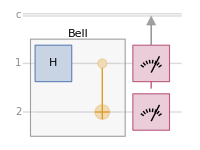
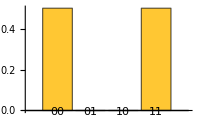
-Graphics- ⇒ -Graphics-

```mathematica
With[{circuit=QuantumCircuitOperator[{"Bell","M"->{1,2}}]},
Row[{circuit["Diagram",ImageSize->{200,Automatic}],circuit[]["ProbabilitiesPlot",ImageSize->200]},Style[" ⇒ ",Bold,20]]
]
```

The circuit above no longer results in the same measurement outcome every time. Instead, it uses a Hadamard and CNOT gate to create a state which gives “00” 50% of the time and “11” 50% of the time. This is the famous Bell state named after physicist John Bell.

-Graphics-

## Bra-Ket Notation

In the formalism of quantum mechanics, how to represent and write down the various concepts is an important question. For some common quantum operations, bra-ket notation is particularly useful. This is also sometimes called Dirac notation after P.A.M. Dirac.

-Graphics-

You can display the bra-ket notation for quantum objects using the "Formula" property.

Below is the bra-ket notation for the NOT operation:

```mathematica
QuantumOperator["NOT"]["Formula"]
```

01+10

You can informally read this as a sum of the form appropriate outputpossible input:

```mathematica
Module[{op,state,res},
op=QuantumOperator["NOT"];
state=QuantumState["0"];
res=op[state];
Grid[{{Style["Operator",ColorData[97][1],20][Style["Input",ColorData[97][2],20]],Style["Result",ColorData[97][3],20]},{Style[TraditionalForm[op],ColorData[97][1],20][Style[TraditionalForm[state],ColorData[97][2],20]],Style[TraditionalForm[res],ColorData[97][3],20]}},Frame->All,Spacings->{2,2}]
]
```

Operator[Input] | Result
(01+10)[0] | 1

If the input matches the 0 state, the output is the 1 state. If the input matches the 1 state, the output is the 0 state.

```mathematica
Module[{op,state,res},
op=QuantumOperator["NOT"];
state=QuantumState["1"];
res=op[state];
Grid[{{Style["Operator",ColorData[97][1],20][Style["Input",ColorData[97][2],20]],Style["Result",ColorData[97][3],20]},{Style[TraditionalForm[op],ColorData[97][1],20][Style[TraditionalForm[state],ColorData[97][2],20]],Style[TraditionalForm[res],ColorData[97][3],20]}},Frame->All,Spacings->{2,2}]
]
```

Operator[Input] | Result
(01+10)[1] | 0

### Example

What is the outcome of applying “CNOT” with the first qubit as control and the third qubit as target to the quantum state 100?

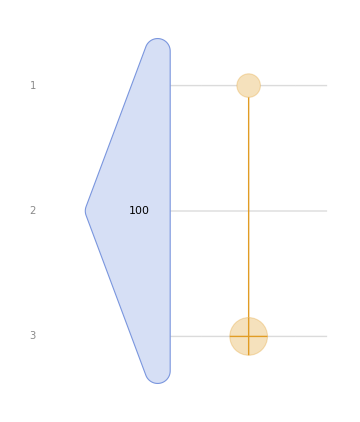

```mathematica
QuantumCircuitOperator[{"100","CNOT"->{1,3}}]["Diagram"]
```

##### Solution

Apply the operator to the specified state:

```mathematica
QuantumOperator["CNOT"->{1,3}][QuantumState["100"]]["Formula"]
```

101

Since the first qubit is initially in the “1” state, the target qubit (third qubit in this case) will be flipped by the controlled operation.

You can get the same result using shorthand circuit notation:

```mathematica
QuantumCircuitOperator[{"100","CNOT"->{1,3}}][]["Formula"]
```

101

## Initialization

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]